```mathematica
Clear["Global`*"]
```

```mathematica
pA={a*Cos[t],0};pB={0,a*Sin[t]};
pAB=pB-pA;
```

```mathematica
pABr=b/a*RotationMatrix[-Pi/2].pAB;
pD=pABr+pA;
{xt,yt}=pD
```

{a Cos[t]+b Sin[t],b Cos[t]}

```mathematica
(b*xt-a*yt)^2+(b*yt)^2-b^4//FullSimplify
```

0

```mathematica
aa=2;bb=4;
```

```mathematica
solxy=Solve[(bb*x-aa*y)^2+(bb*y)^2==bb^4,Integers];
pt={x,y}/.solxy
```

{{-4,0},{-2,-4},{2,4},{4,0}}

```mathematica
g1=ParametricPlot[{aa*Cos[t]+bb*Sin[t],bb*Cos[t]},{t,0,2*Pi},GridLines->{Table[i,{i,-4,4}],Table[j,{j,-4,4}]},Ticks->{Table[i,{i,-5,5}],Table[j,{j,-5,5}]},PlotRange->{{-5,5},{-5,5}},PlotStyle->Thickness[0.006],AspectRatio->Automatic,ImageSize->Large];
```

```mathematica
g2=Graphics[{EdgeForm[{Thick,Orange}],FaceForm[],Translate[Rotate[Rectangle[{0,0},{aa,bb}],-Pi/4,{0,0}],{0,aa/Sqrt[2]}]}];
```

```mathematica
g3=Graphics[{Thick,EdgeForm[{Thick,Orange}],FaceForm[White],Disk[{(aa+bb)/Sqrt[2],bb/Sqrt[2]},0.08]}];
```

```mathematica
g4=Graphics[{PointSize[0.015],Black,Point[pt]}];
```

```mathematica
g5=Graphics[{Text[Style["O",FontFamily->"Times New Roman",Italic,20],{-0.2,-0.2}],
Text[Style["A",FontFamily->"Times New Roman",Italic,20],{1.3,-0.2}],
Text[Style["B",FontFamily->"Times New Roman",Italic,20],{-0.2,1.4}],
Text[Style["C",FontFamily->"Times New Roman",Italic,20],{2.7,4.4}],
Text[Style["D",FontFamily->"Times New Roman",Italic,20],{4.5,3}]}];
```

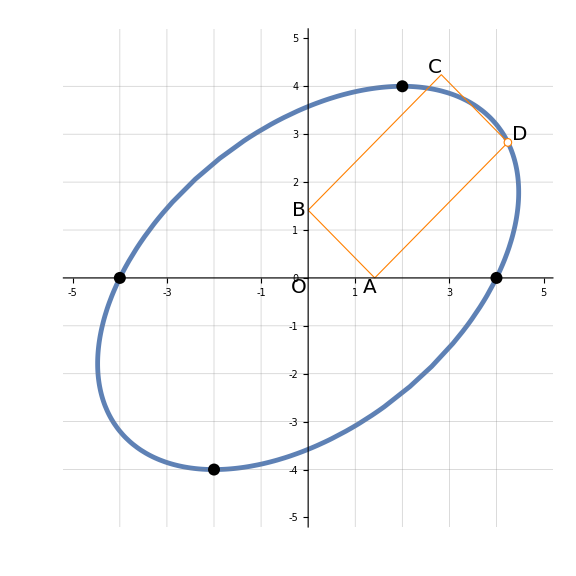

```mathematica
Show[g1,g2,g3,g4,g5]
```